# Table of Contents

## Introduction

In this project, an original scheme for secure image communication is presented, which combines the conventional DES cryptography algorithm with a chaotic signal generator based on a 3-order cellular neural network. A detailed simulation is conducted using the Wolfram Mathematica 7 software, the results of which indicate that many of the shortcomings of both purely-algebraic cryptography and purely-chaos-based cryptography have been addressed. In particular, for many applications, the scheme presented is more suitable than the DES algorithm alone.

Part I provides an overview of chaotic dynamics, cellular neural networks and the 3-order CNN, with illustrative simulations of their dynamical properties. Part II applies these concepts to the secure image communication scheme, which is discussed and simulated in some detail. Finally, the appendix contains an implementation of the DES algorithm.

The entire project documentation was prepared in Wolfram Mathematica 7.

## Part I: Chaos and cellular neural networks

### Overview of chaotic dynamics

#### Dynamical systems

A dynamical system may be defined as a deterministic mathematical prescription for evolving the state of a system forward in time. Time here (denoted t) may be a continuous variable or a discrete integer-valued variable.

An example in the former case is a system of N first-order autonomous ordinary differential equations

(ⅆx(t))/ⅆt=F[x(t)],

where x is an N-dimensional vector.

An example in the latter case is a map

x_(t+1)=M(x_t), t=0,1,2,…,

where x_t is an N-dimensional vector.

#### Chaos

When N⩾3 for a system of first-order autonomous ordinary differential equations, N⩾2 for an invertible map and N⩾1 for a non-invertible map, the trajectory of the system in N-dimensional phase space may be neither steady nor periodic (nor quasi-periodic), and such that it cannot be represented using standard analytical functions. Most such systems are said to exhibit the stable pseudo-random state of chaos.

#### Attractors

If ∇·F<0 for a system of first-order autonomous ordinary differential equations in some region of phase space, or the magnitude of the determinant of the Jacobian matrix of partial derivatives of a map is lesser than unity in some region of phase space, both signifying N-dimensional phase space volume contraction in that region, the system is said to be dissipative.

Dissipative systems typically are characterized by the presence of attracting sets or attractors in the phase space. These are bounded subsets to which regions of initial conditions of non-zero phase space volume asymptote as time increases.

It is a characteristic of chaotic dynamics that the resulting attractors commonly have a non-integer box-counting dimensionality. Such geometrical objects are called fractals. When an attractor is fractal, it is called a strange attractor. Thus most chaotic attractors are strange, with the notable exception of most one-dimensional maps.

#### Sensitive dependence on initial conditions

A defining attribute of an attractor on which the dynamics is chaotic is that it displays exponentially sensitive dependence on initial conditions. This sensitivity is measured by its Lyapunov exponents, given by:

λ_i=lim_(t→∞,|Δx_i0|→0) 1/t ln(|Δx_i(x_i0,t)|)/(|Δx_i0|)

If there is at least one positive Lyapunov exponent and the sum of all Lyapunov exponents is negative, the dynamics on the attractor is chaotic.

Due to sensitive dependence, small errors in the solution can grow very rapidly. In time, effects such as noise and computer roundoff can totally change the solution. Hence, sensitivity to changes in initial conditions implies sensitivity to changes in computational precision. Given the state of a chaotic system, its future becomes difficult to predict after a certain point, computing at a limited precision.

#### Simulation: the Lorenz model

The problem of chaotic Rayleigh-Benard convection was originally studied theoretically and computationally in the seminal paper of Lorenz. The Lorenz model is an approximation to partial differential equations describing the turbulent flow of convective currents in a fluid layer heated from below:

ⅆx/ⅆt=p(y-x)
				ⅆy/ⅆt=qx-y-xz
				ⅆz/ⅆt=xy-rz

The constants p, q and r are positive. The variable x is the amplitude of the convective currents, y is the temperature difference between rising and falling currents and z is the deviation from the normal temperatures. So:

```mathematica
vars={x[t],y[t],z[t]};

f=p(y[t]-x[t]);
g=q x[t]-y[t]-x[t]z[t];
h=x[t]y[t]-r z[t];

eqns={x'[t]==f,y'[t]==g,z'[t]==h};
```

The equilibrium points are as follows:

```mathematica
equi=Solve[{f==0,g==0,h==0},vars]
```

{{y[t]→0,z[t]→0,x[t]→0},{y[t]→-√((-1+q) r),z[t]→-1+q,x[t]→-√(-r+q r)},{y[t]→√(-r+q r),z[t]→-1+q,x[t]→√(-r+q r)}}

Defining the following numerical values for the constants,

```mathematica
p=3;q=268/10;r=1;
```

the equilibrium points are now:

```mathematica
equi//N
```

{{y[t]→0.,z[t]→0.,x[t]→0.},{y[t]→-5.07937,z[t]→25.8,x[t]→-5.07937},{y[t]→5.07937,z[t]→25.8,x[t]→5.07937}}

To demonstrate the sensitivity to changes in computational precision, three different solutions are computed with successively tighter precision and accuracy conditions:

```mathematica
inits={x[0]==0,y[0]==1,z[0]==0};

sol1=vars/.NDSolve[Join[eqns,inits],vars,{t,0,35}][[1]];
sol2=vars/.NDSolve[Join[eqns,inits],vars,{t,0,35},WorkingPrecision->25,PrecisionGoal->12,AccuracyGoal->12][[1]];
sol3={sx,sy,sz}=vars/.NDSolve[Join[eqns,inits],vars,{t,0,35},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->13000][[1]];
```

Comparing the first and second solutions:

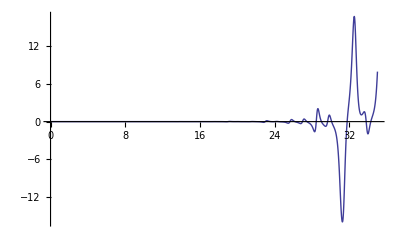
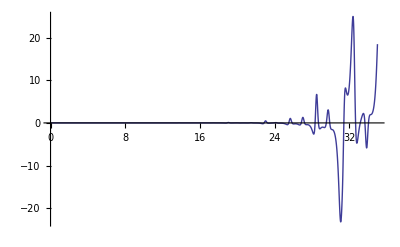
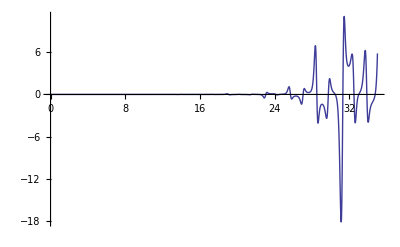

```mathematica
Plot[#,{t,0,35},PlotRange->All]&/@(sol1-sol2)
```

Comparing the second and third solutions:

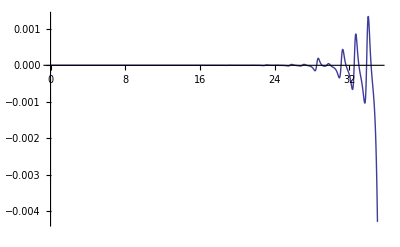
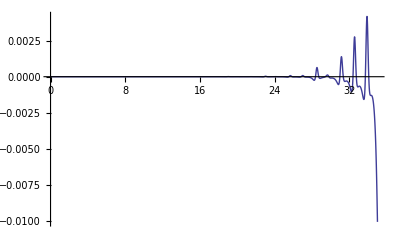
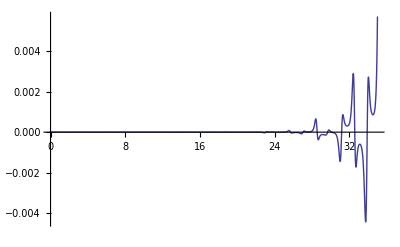

```mathematica
Plot[#,{t,0,35},PlotRange->All]&/@(sol2-sol3)
```

We see that the first two solutions differ greatly from approximately t=25 onwards, and the last two from approximately t=30 onwards. This sensitivity makes the prediction of a chaotic system impossible after a certain point, due to limited computational precision.

To demonstrate the sensitivity to initial conditions, we solve the equations by very slightly changing z(0), and compare the solution to the previously obtained one:

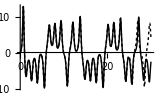

```mathematica
sol4=vars/.NDSolve[Join[eqns,{x[0]==0,y[0]==1,z[0]==10^-5}],vars,{t,0,35},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->13000][[1]];

Plot[Evaluate[{sol3[[1]],sol4[[1]]}],{t,0,30},PlotStyle->{{Black,Dashing[{Tiny}]},{Black}},ImageSize->160]
```

We see that the solutions differ greatly from approximately t=29 onwards. This sensitivity makes the prediction of a chaotic system impossible after a certain point, since the initial conditions are hardly known exactly.

Plotting the three curves in the same figure:

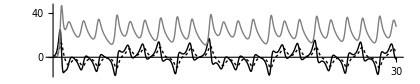

```mathematica
Plot[sol3,{t,0,30},Ticks->{{30},Automatic},PlotStyle->{{Black,Dashing[{Tiny}]},{Black},{Gray}},ImageSize->420,AspectRatio->0.2]
```

and in three separate figures:

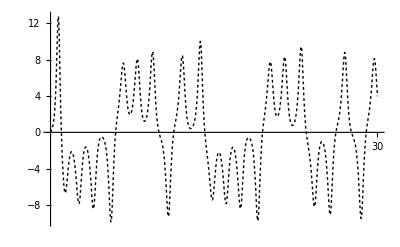
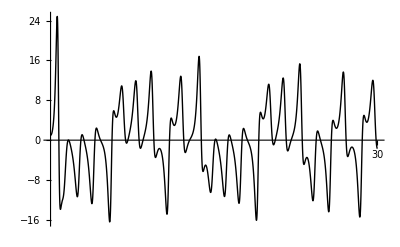
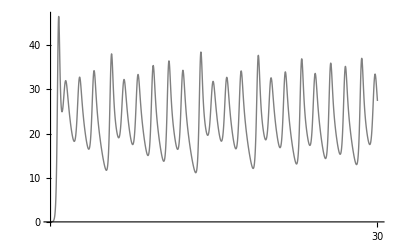

```mathematica
MapThread[Plot[#1,{t,0,30},PlotStyle->#2,Ticks->{{30},Automatic}]&,{sol3,{{Black,Dashing[{Tiny}]},{Black},{Gray}}}]
```

We notice that the components seem to evolve quite unpredictably and chaotically. However, the pairwise plane trajectories reveal the existence of attractors:

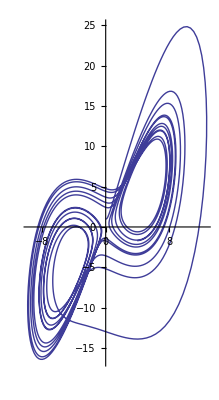
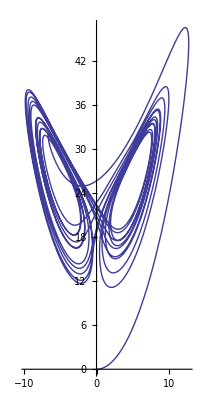
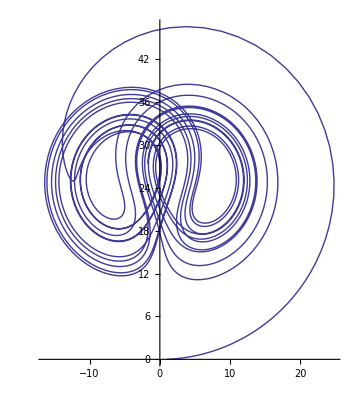

```mathematica
ParametricPlot[#,{t,0,30}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

Finally, the space trajectory is plotted. A two-image stereo-gram is produced, which involves two versions of the figure with slightly different viewpoints. To prevent the figure from becoming too complex, I have plotted only till t=10.5. By superimposing the two figures by focusing the eyes behind the paper, it is possible to get an amazing stereoscopic view:

```mathematica
GraphicsRow[ParametricPlot3D[sol3, {t, 0, 10.5}, ViewPoint -> #] & /@ {{1.3, -2.4, 0.8}, {1.4, -2.3, 0.8}}, ImageSize -> 280, Spacings -> -80]
```

-Graphics-

We can also plot points along the trajectory. This gives an impression of the speed of the process:

```mathematica
GraphicsRow[Graphics3D[{PointSize[Tiny],Darker[Blue],Point[Table[sol3,{t,0,10.5,0.03}]]},ViewPoint->#]&/@{{1.3,-2.4,0.8},{1.4,-2.3,0.8}},ImageSize->280,Spacings->-80]
```

-Graphics-

### Overview of the cellular neural network

#### Background

CNN was first introduced as an acronym for Cellular Neural Network by Chua and Yang [6]. It is an information or signal processing system composed of a large number of simple analog processing elements, called cells, which are locally interconnected and perform parallel processing in order to solve a given computational task. The key concept that distinguishes a CNN from other neural networks is that the inter-connections among cells are local. This makes CNN models tailor-made for monolithic implementation in currently available planar technologies. Since its invention many applications of CNNs have been presented in literature, especially for image-processing tasks [e.g. xrx].

Chua and Roska also interpreted CNN as Cellular Nonlinear Network. In this way the original paradigm was extended and employed also for generating chaotic and hyper-chaotic signals, static and dynamic patterns, auto-waves, spiral waves and spatial-temporal chaos. From an engineering point of view, CNN characterizes a network consisting of locally coupled nonlinear dynamical systems to generate certain behavior or to process information. CNNs are used for processing as well as producing information. Furthermore, these two purposes are also combined in coupled local minimizers and coupled chaotic annealing process.

Definition: A CNN is any spatial arrangement of locally-coupled cells, where each cell is a dynamical system which has an input, an output and a state evolving according to some prescribed dynamical laws.

The resulting network is defined mathematically by four specifications: cell dynamics, the synaptic law, boundary conditions and initial conditions. A one-dimensional and a two-dimensional CNN architecture is a spatial arrangement of a locally-coupled row of N cells and N×M array of cells, respectively. For a continuous-time CNN, cells usually consist of time-invariant circuit elements and can be any dynamical system. A 3-D CNN can be built up by cascading 2-D CNN layers.

#### The Chua-Yang model

The original CNN model was introduced by Chua and Yang [6]. Since then, stability analysis of this model has been extensively studied [4]. Furthermore, bifurcation phenomena and chaotic behavior have been investigated and a chaotic attractor has been observed in the dynamics. The Chua-Yang model is still a widely used model.

The cell dynamics of the Chua-Yang CNN model are governed by the following state equations:

(ẋ)_(i,j)=-x_(i,j)+a_(0,0)y_(i,j)+b_(0,0)u_(i,j)+z+I_(i,j)^s
			y_(i,j)=f(x_(i,j))=1/2(|x_(i,j)+1|-|x_(i,j)-1|),

where x_(i,j),y_(i,j),u_(i,j),z,I_(i,j)^s∈ℝ (first order cells).

The synaptic law of the model is given by:

I_(i,j)^s=∑_(k,l∈S_(i,j)) a_(k-i,l-j)y_(k,l)+b_(k-i,l-j)u_(k,l)

A fixed boundary condition was proposed by Chua and Yang [6]. The CNN is clamped at its ends to value 0. However, other boundary conditions can be used as well.

#### The CNN Universal Machine: a visual microprocessor

The CNN paradigm has provided an ideal framework for programmable analog array computing. It means that the CNN can be used as a programmable device where the instructions are represented by the templates. This was the key idea in proposing the CNN universal machine (CNN-UM) which is the first algorithmically programmable analog array computer. Another aspect which distinguishes the CNN-UM from a conventional digital computer is the dual computing capability. Dual computing combines analog array processing with logic operations, therefore named as analogic (which is a contraction of analog and logic computation) computing by Roska and Chua. Universality of the CNN Universal Machine has been proved by Roska & Chua and Crounse & Chua in the sense of Turing, meaning that it is able to realize any recursive function. In order to avoid input/output connections with the external world on the CNN-UM, Roska and Chua proposed the integration of an array of sensors on the same chip.

From an application point of view, the CNN universal chip allows to use the algorithm introduced as an efficient preprocessing procedure for many interesting image/video applications such as skeletonizing, segmentation, watermarking, the binary and gray-scale morphological erosion, dilation, and reconstruction operators and many others. For these operations, there is already an image processing library which contains a collection of designed templates.

### The 3-order CNN

#### Model definition

Here, a 3-order CNN dynamic model with full connecting [9] has been selected. This is the simplest CNN which exhibits chaotic phenomena:

OverDot[x_i]=-x_i+a_i y_i+∑_(k=1,k≠i)^3 a_ik y_i+∑_(k=1)^3 s_ik x_k+I_i, i=1,2,3,

where x_i is the state variable of cell i and y_i denotes the output of cell i, which is defined as:

y_i=0.5(|x_i+1|-|x_i-1|), i=1,2,3

Let the cell template parameters be:

a_12=a_13=a_2=a_23=a_32=a_3=a_21=a_31=0
				s_13=s_31=s_22=I_1=I_2=I_3=0
				s_21=s_23=s_33=1

Then, we get from (7):

OverDot[x_1]=a_1 y_1+s_11 x_1+s_12 x_2-x_1
				OverDot[x_2]=x_1-x_2+x_3
				OverDot[x_3]=s_32 x_2

And from (8):

y_1=0.5(|x_1+1|-|x_1-1|)

So:

```mathematica
vars={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t]};

f=-Subscript[x, 1][t]+Subscript[a, 1]*5/10*(Abs[Subscript[x, 1][t]+1]-Abs[Subscript[x, 1][t]-1])+Subscript[s, 11] Subscript[x, 1][t]+Subscript[s, 12] Subscript[x, 2][t];
g=-Subscript[x, 2][t]+Subscript[x, 1][t]+Subscript[x, 3][t];
h=Subscript[s, 32] Subscript[x, 2][t];

eqns={Subscript[x, 1]'[t]==f,Subscript[x, 2]'[t]==g,Subscript[x, 3]'[t]==h};
```

#### Dissipativity and existence of attractors

It follows from the previous discussion of dissipativity that this model must satisfy the inequality

∇V=(∂OverDot[x_1])/(∂x_1)+(∂OverDot[x_2])/(∂x_2)+(∂OverDot[x_3])/(∂x_3)<0

in order to be dissipative. Then:

```mathematica
grad=D[f, Subscript[x, 1]]+D[g, Subscript[x, 2]]+D[h, Subscript[x, 3]]
```

-2 1[t]+1[t] s_11+1/2 a_1 (-1[t] Abs'[-1+x_1[t]]+1[t] Abs'[1+x_1[t]])

When |x_1|>1:

```mathematica
FullSimplify[grad,Subscript[x, 1][t]>1||Subscript[x, 1][t]<-1]
```

1[t] (-2+s_11)

Hence for all s_11<2, the system is dissipative, with an exponential contraction rate e^(s_11-2). That is, a volume element V_0 is contracted by the flow into a volume element V_0 e^((s_11-2)t) in time t. Thus, each volume containing the system trajectory shrinks to zero as t→∞ at an exponential rate s_11-2. The system orbits are ultimately confined into a specific limit set of zero volume, and the system asymptotic motion settles onto an attractor.

When |x_1|⩽1:

```mathematica
FullSimplify[grad,Subscript[x, 1][t]<1&&Subscript[x, 1][t]>-1]
```

1[t] (-2+a_1+s_11)

Hence for all a_1+s_11<2, the system is dissipative, with an exponential contraction rate e^(a_1+s_11-2). That is, a volume element V_0 is contracted by the flow into a volume element V_0 e^((a_1+s_11-2)t) in time t. Thus, each volume containing the system trajectory shrinks to zero as t→∞ at an exponential rate a_1+s_11-2. The system orbits are ultimately confined into a specific limit set of zero volume, and the system asymptotic motion settles onto an attractor.

#### Simulation

The dynamical behavior of the above model will now be simulated. We mirror the previous simulation of the Lorenz model, thereby facilitating comparison between the two models.

Choosing the parameters a_1=3.86,s_11=-1.55,s_12=8.98,s_32=-14.26 and the initial conditions x(0)=[0.2,0.2,0.2]:

```mathematica
inits={Subscript[x, 1][0]==2/10,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10};

Subscript[a, 1]=386/100;Subscript[s, 11]=-155/100;Subscript[s, 12]=898/100;Subscript[s, 32]=-1426/100;
```

```mathematica
sol1=vars/.NDSolve[Join[eqns,inits],vars,{t,0,50}]⟦1⟧;
sol2=vars/.NDSolve[Join[eqns,inits],vars,{t,0,50},WorkingPrecision->25,PrecisionGoal->12,AccuracyGoal->12]⟦1⟧;
sol3={sx,sy,sz}=vars/.NDSolve[Join[eqns,inits],vars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
sol4=vars/.NDSolve[Join[eqns,{Subscript[x, 1][0]==2001/10000,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10}],vars,{t,0,40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->13000]⟦1⟧;
```

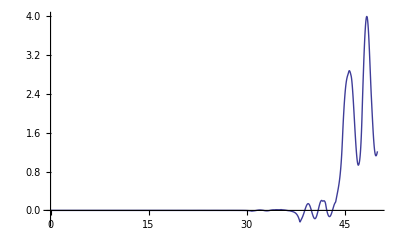
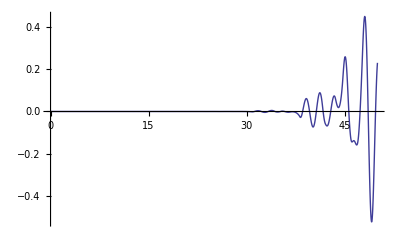
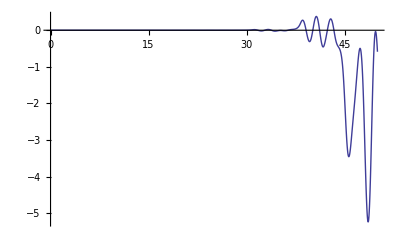

```mathematica
Plot[#,{t,0,50},PlotRange->All]&/@(sol1-sol2)
```

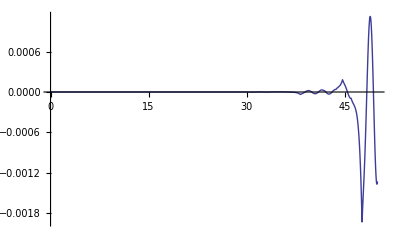
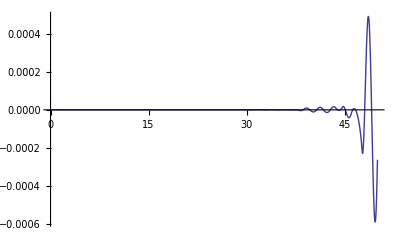
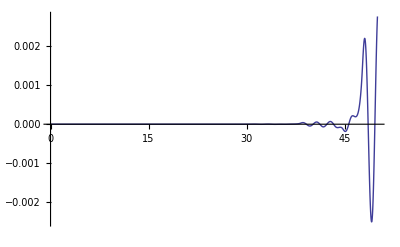

```mathematica
Plot[#,{t,0,50},PlotRange->All]&/@(sol2-sol3)
```

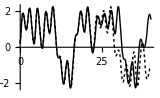

```mathematica
Plot[Evaluate[{sol3⟦1⟧,sol4⟦1⟧}],{t,0,40},PlotStyle->{{Black,Dashing[{Tiny}]},{Black}},ImageSize->160]
```

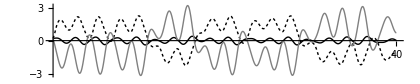

```mathematica
Plot[sol3,{t,0,40},Ticks->{{40},Automatic},PlotStyle->{{Black,Dashing[{Tiny}]},{Black},{Gray}},ImageSize->420,AspectRatio->0.2]
```

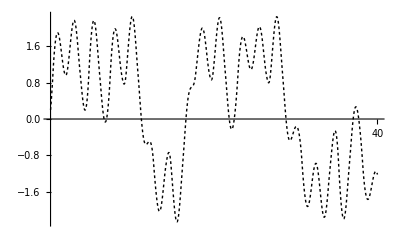
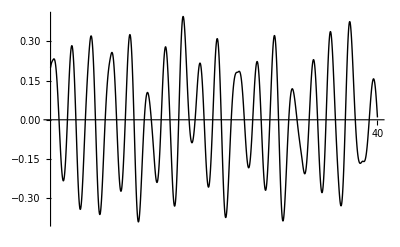
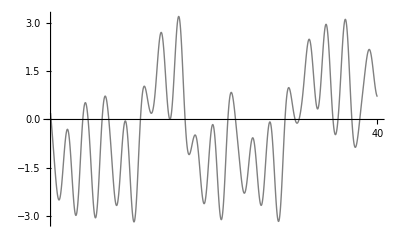

```mathematica
MapThread[Plot[#1,{t,0,40},PlotStyle->#2,Ticks->{{40},Automatic}]&,{sol3,{{Black,Dashing[{Tiny}]},{Black},{Gray}}}]
```

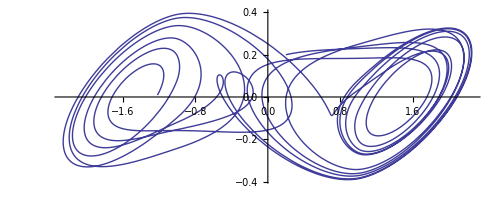
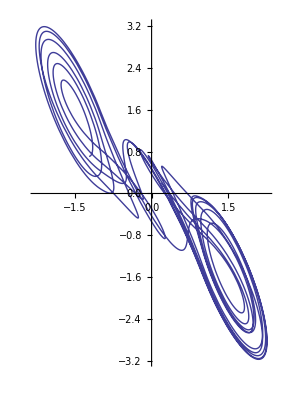
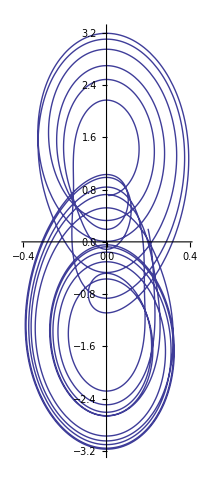

```mathematica
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

By choosing different parameters, different characteristic chaotic attractors are gained:

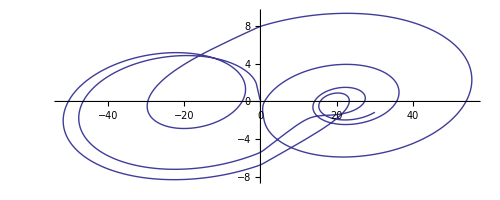
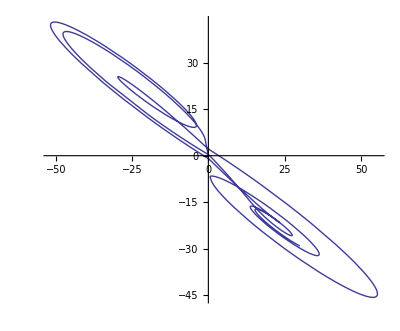
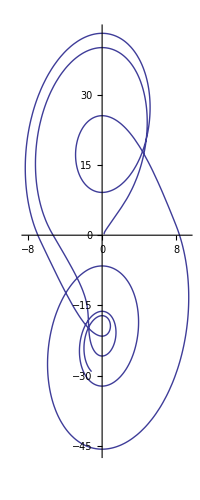

```mathematica
Subscript[a, 1]=-7717/1000;Subscript[s, 11]=13443/10000;Subscript[s, 12]=-4925/1000;Subscript[s, 32]=3649/1000;
sol3={sx,sy,sz}=vars/.NDSolve[Join[eqns,inits],vars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

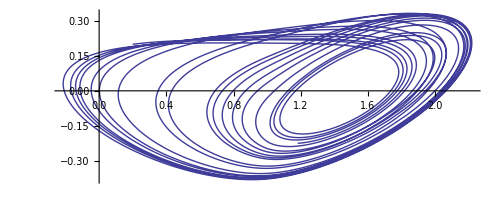
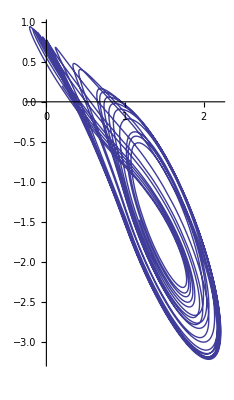
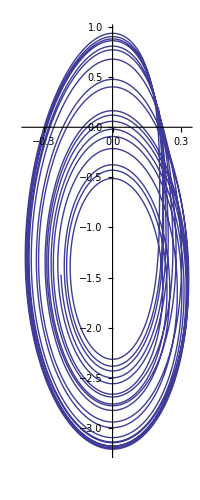

```mathematica
Subscript[a, 1]=40279/10000;Subscript[s, 11]=-16856/10000;Subscript[s, 12]=94/10;Subscript[s, 32]=-16;
sol3={sx,sy,sz}=vars/.NDSolve[Join[eqns,inits],vars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

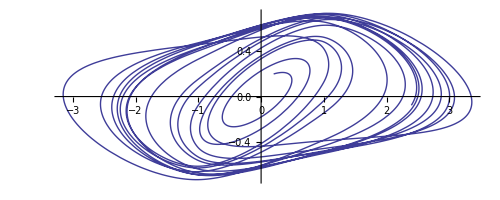
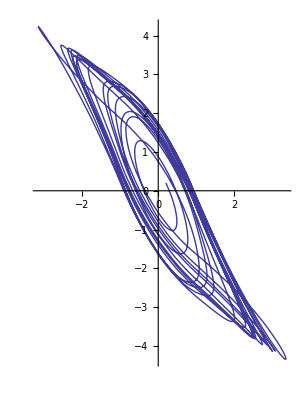
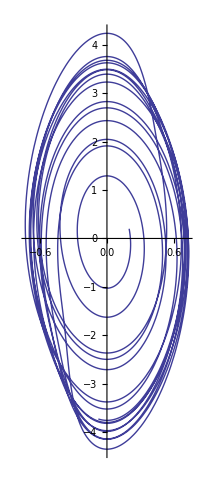

```mathematica
Subscript[a, 1]=-36805/10000;Subscript[s, 11]=22179/10000;Subscript[s, 12]=8342/1000;Subscript[s, 32]=-11925/1000;
sol3={sx,sy,sz}=vars/.NDSolve[Join[eqns,inits],vars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

## Part II: An application

### Chaos and cryptography

#### Cryptographic properties of chaotic systems

The idea of using chaos for data encryption can be traced to Shannon, who suggested using measure-preserving transformations which depend on their arguments in a sensitive way. Although chaotic dynamical systems are linearly unstable, they have synchronization properties. Furthermore, the following features make them promising candidates for constructing cryptographic systems:

1) Sensitive dependence on initial conditions (already discussed) ensures that if the initial conditions used to encrypt data are changed by even a small amount, the encrypted data is wildly different. As a result, an attack aiming to exploit a pattern in the encrypted data by trying out numerous initial conditions (i.e. a brute force attack) cannot succeed.

2) Ergocidy implies that the phase space cannot be non-trivially divided into several parts. That is, if a trajectory starts from some point, it never localizes in a smaller region. Knowing the final state of the system we can never identify the smaller region where the trajectory started. Ergocidy ensures the spreading of the initial region over the entire phase space. Thus, the influence of a single plain-text digit spreads over many cipher-text digits.

3) Mixing implies that a trajectory started at some point, after sufficiently many iterations, reaches all regions in the phase space with equal probability. Mixing ensures the resistance of a cryptographic system against statistical attack.

The preceding features ensure that chaotic encryption systems satisfy the classic Shannon requirements of confusion and diffusion.

#### Comparison of classical and chaotic cryptography

Classical cryptography works on discrete values and in discrete time while chaotic cryptography works on continuous-value systems that may operate in continuous or discrete time. Classical cryptography is characterized by integer values on finite fields, algebraic methods and digital realization by integer arithmetic. Chaotic cryptography is correspondingly characterized by continuous values using fixed or floating point representation, analytic methods and digital realization by non-integer arithmetic. Similarities include sensitivity to initial conditions and parameters, pseudo-random behavior and unstable orbits with very long periods, depending upon the precision of the numerical implementation.

According to several authors, an extension of the domain of a classical encryption algorithm from a finite field to a continuum will give rise to a chaotic map. For example, the domain extension for the round function of the DES algorithm was proved to be a chaotic map.

### A scheme for secure image communication

#### Motivation

Although algebraic cryptography algorithms such as DES can be applied to image cryptography, they are easily attacked because of their short encryption key. Public encryption algorithms can provide a long key, but are unsuitable for image encryption due to their slow speed. Also, established cryptanalytic techniques exist against these algorithms, such as linear and differential cryptanalysis.

Chaotic encryption schemes have traditionally used discrete-time chaotic systems, typically the logistic map. Also, [13] uses a feedback-enabled logistic map and [7] combines a logistic map with a CNN. However, general methods of attack [11, 12] have been devised against such systems. Also, the design of the key space is flawed and it is difficult to estimate the security compared to conventional encryption schemes.

Importantly, [14] concludes from statistical analysis that chaos is a necessary but not sufficient property of encryption algorithms and that the best results will be obtained by combining classical and chaotic cryptographic techniques. The applications suggested are auto-synchronized cryptographic algorithms and the implementation of non-linear substitution boxes (S-boxes) using discretized chaotic maps. Along these lines, [15] suggests combining an elementary map with an XOR operation. It concludes that the resulting hybrid algorithm is highly resistant to a brute-force attack.

In light of the above discussion, an algorithm adopting a 3-order CNN as the chaotic signal generator, combined with the conventional encryption algorithm DES, is presented according the idea in [10].

#### Block diagram

#### Algorithm

1) c=p⊕x where x_j=round(K √(x_(1j)^2+x_(2j)^2+x_(3j)^2)+λ)  mod 256 where x_(1j), x_(2j) and x_(3j) are the numerical solutions of state variables in (10) on time j. x is composed of x_(j mod A). The constants K, λ and A are control parameters.
2) d=DES_k(c)
3) We assume perfect transmission over the channel for the purposes of this simulation.
4) c=DES_k^-1(d)
5) p=x⊕c

The entire process is summarized by the equations:

p=x⊕DES_k^-1[DES_k(p⊕x)]

### Detailed simulation and analysis of results

#### CNN encryption

Three solutions of the system of equations are obtained: sol3 is used to encrypt the image, and correctly decrypt it; sol4 incorporates a slight change in the initial conditions, and is used to demonstrate the sensitivity of the decryption to such a change; sol5 incorporates a slight change in computational precision, and is used to demonstrate the sensitivity of the decryption to that change.

```mathematica
vars={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t]};

f=-Subscript[x, 1][t]+Subscript[a, 1]*5/10*(Abs[Subscript[x, 1][t]+1]-Abs[Subscript[x, 1][t]-1])+Subscript[s, 11] Subscript[x, 1][t]+Subscript[s, 12] Subscript[x, 2][t];
g=-Subscript[x, 2][t]+Subscript[x, 1][t]+Subscript[x, 3][t];
h=Subscript[s, 32] Subscript[x, 2][t];

eqns={Subscript[x, 1]'[t]==f,Subscript[x, 2]'[t]==g,Subscript[x, 3]'[t]==h};
inits={Subscript[x, 1][0]==2/10,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10};
Subscript[a, 1]=386/100;Subscript[s, 11]=-155/100;Subscript[s, 12]=898/100;Subscript[s, 32]=-1426/100;
K=3000;λ=127;A=256;

sol3=vars/.NDSolve[Join[eqns,inits],vars,{t,0,A+40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->45000]⟦1⟧;
sol4=vars/.NDSolve[Join[eqns,{Subscript[x, 1][0]==2001/10000,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10}],vars,{t,0,A+40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->45000]⟦1⟧;
sol5=vars/.NDSolve[Join[eqns,inits],vars,{t,0,A+40},WorkingPrecision->24,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->45000]⟦1⟧;
```

The constant A determines the number of pseudo-random values used in CNN-encryption (and CNN-decryption). It is a measure of the robustness of the cipher-image, and may be increased (up to the total number of pixels in the plain-image), at the cost of computational expense.

```mathematica
image=-Graphics-;
plaintext=Flatten[ImageData[image,"Byte"]];cols=ImageDimensions[image]⟦1⟧;
```

CNN encryption:

```mathematica
f={};
Do[AppendTo[f,sol3/.t->(i+40)],{i,1,A}]

CNNciphertext={};Do[r=Mod[Round[K√((f⟦Mod[i,A]+1,1⟧)^2+(f⟦Mod[i,A]+1,2⟧)^2+(f⟦Mod[i,A]+1,3⟧)^2)+λ],256];AppendTo[CNNciphertext,BitXor[plaintext⟦i⟧,r]],{i,1,Length[plaintext]}]
```

Pseudo random values at t<41 are not used, since from the plots in Part I, it may be observed that these values are comparatively less sensitive to changes in computational precision.

Result of the CNN encryption:

```mathematica
Image[Partition[Partition[CNNciphertext,3],cols],"Byte"]
```

-Graphics-

#### DES encryption

```mathematica
CNNciphertext=Flatten[ImageData[-Graphics-,"Byte"]];
DESkey=Import["C:\\Users\\Atriya\\Documents\\key.txt","Byte"];
```

The following 64-bit key has been used: 3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&

```mathematica
prepared={};
Do[AppendTo[prepared,IntegerDigits[CNNciphertext⟦i⟧,2,8]],{i,1,Length[CNNciphertext]}]
prepared=Partition[Flatten[prepared],64,64,1,0];
```

DES encryption:

```mathematica
processed={};
Do[AppendTo[processed,DESEncrypt[prepared⟦i⟧,DESkey]],{i,1,Length[prepared]}]
```

```mathematica
DESciphertext={};
temp=Partition[Flatten[processed],8];
Do[AppendTo[DESciphertext,FromDigits[temp⟦i⟧,2]],{i,1,Length[temp]}]
```

Result of the DES encryption:

```mathematica
Image[Partition[Partition[DESciphertext,3],cols],"Byte"]
```

-Graphics-

In a practical implementation, this image would now be transmitted over the insecure communication channel.

#### DES decryption

```mathematica
prepared={};
Do[AppendTo[prepared,IntegerDigits[DESciphertext⟦i⟧,2,8]],{i,1,Length[DESciphertext]}]
prepared=Partition[Flatten[prepared],64];
```

DES decryption:

```mathematica
processed={};
Do[AppendTo[processed,DESDecrypt[prepared⟦i⟧,DESkey]],{i,1,Length[prepared]}]
```

```mathematica
DESdeciphertext={};
temp=Partition[Flatten[processed],8];Do[AppendTo[DESdeciphertext,FromDigits[temp⟦i⟧,2]],{i,1,Length[temp]}]
```

Result of the DES decryption:

```mathematica
Image[Partition[Partition[DESdeciphertext,3],cols],"Byte"]
```

-Graphics-

#### CNN decryption

```mathematica
DESdeciphertext=Flatten[ImageData[-Graphics-,"Byte"]];
CNNdeciphertext={};
CNNdeciphertextwrong={};
CNNdeciphertextwrong2={};
```

CNN decryption:

```mathematica
f={};
Do[AppendTo[f,sol3/.t->(i+40)],{i,1,A}]

Do[r=Mod[Round[K√((f⟦Mod[i,A]+1,1⟧)^2+(f⟦Mod[i,A]+1,2⟧)^2+(f⟦Mod[i,A]+1,3⟧)^2)+λ],256];AppendTo[CNNdeciphertext,BitXor[r,DESdeciphertext⟦i⟧]],{i,1,Length[DESdeciphertext]}]
```

```mathematica
f={};
Do[AppendTo[f,sol4/.t->(i+40)],{i,1,A}]

Do[r=Mod[Round[K√((f⟦Mod[i,A]+1,1⟧)^2+(f⟦Mod[i,A]+1,2⟧)^2+(f⟦Mod[i,A]+1,3⟧)^2)+λ],256];AppendTo[CNNdeciphertextwrong,BitXor[r,DESdeciphertext⟦i⟧]],{i,1,Length[DESdeciphertext]}]
```

```mathematica
f={};
Do[AppendTo[f,sol5/.t->(i+40)],{i,1,A}]

Do[r=Mod[Round[K√((f⟦Mod[i,A]+1,1⟧)^2+(f⟦Mod[i,A]+1,2⟧)^2+(f⟦Mod[i,A]+1,3⟧)^2)+λ],256];AppendTo[CNNdeciphertextwrong2,BitXor[r,DESdeciphertext⟦i⟧]],{i,1,Length[DESdeciphertext]}]
```

Correct decryption:

```mathematica
Image[Partition[Partition[CNNdeciphertext,3],cols],"Byte"]
```

-Graphics-

Unrecognizable decryption due to a slight change in the initial conditions:

```mathematica
Image[Partition[Partition[CNNdeciphertextwrong,3],cols],"Byte"]
```

-Graphics-

Unrecognizable decryption due to a slight change in computational precision:

```mathematica
Image[Partition[Partition[CNNdeciphertextwrong2,3],cols],"Byte"]
```

-Graphics-

We observe that the results are extremely sensitive to changes in both the precision of the computation and the initial conditions. The chaotic signals used in the CNN-encryption are obtained after rounding, taking modulus, squaring, evolution, magnification and excursion, and are different from the original chaotic sequences. The security is increased because of the complex calculation involved and the parameters. This hybrid algorithm is not only a remedy for the small key space of the DES algorithm, but also resists the attacks on chaotic encryption systems by determining initial conditions outlined in [11] and [12]. Thus, security is increased on the whole. The scheme is also suitable for encryption of text, audio and video.

#### Correctness test

A bitwise comparison of the original and decrypted image is performed:

```mathematica
plaintext==CNNdeciphertext
```

True

#### Complexity test

```mathematica
data={};
throwaway={};
```

We plot a graph of the plain-image size (in pixels) against the total time (in seconds) required to CNN-encrypt it:

```mathematica
Do[image=ImageResize[-Graphics-,Scaled[1/j]];imagetext=Flatten[ImageData[image,"Byte"]];AppendTo[data,Timing[f={};Do[AppendTo[f,sol3/.t->(i+40)],{i,1,A}];Do[r=Mod[Round[K√((f⟦Mod[i,A]+1,1⟧)^2+(f⟦Mod[i,A]+1,2⟧)^2+(f⟦Mod[i,A]+1,3⟧)^2)+λ],256];AppendTo[throwaway,BitXor[imagetext⟦i⟧,r]],{i,1,Length[imagetext]}]]⟦1⟧];AppendTo[data,ImageDimensions[image]⟦1⟧*ImageDimensions[image]⟦2⟧],{j,1,10}]
```

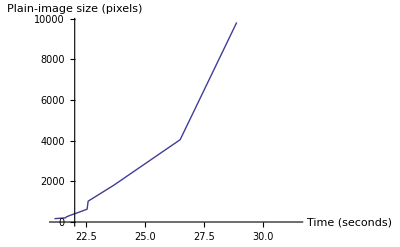

```mathematica
ListLinePlot[Partition[data,2],AxesLabel->{"Time (seconds)","Plain-image size (pixels)"}]
```

We observe that even for large increases in image size, the increase in the total time required is very modest. Moreover, this increase is reduced even further at large image sizes. However, this is because at small image sizes, the time required to perform the XOR operation is insignificant compared to the time required to obtain the pseudo-random values. Internal optimizations by the Mathematica kernel may also be partially responsible.

#### Statistical analysis

Shannon showed that many encryption schemes can be attacked by statistical analysis. He proposed that such attacks could be resisted by improving confusion and diffusion properties. It is most advantageous if the cipher-image bears little or no statistical resemblance to the plain-image.

Histogram of the plain-image:

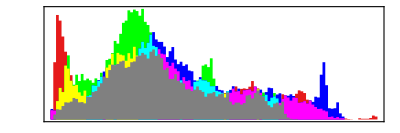

```mathematica
ImageHistogram[-Graphics-]
```

Large spikes are observed around the green and red colours, corresponding to the high amount of these colours in the plain-image.

Histogram of the cipher-image:

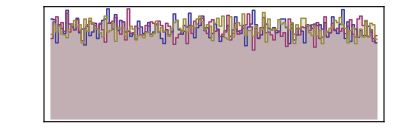

```mathematica
ImageHistogram[-Graphics-]
```

It is observed that the cipher-image histogram has the feature of equality, which signifies high confusion and diffusion and makes it resistant to statistical attack. Also, the magnitude of the peaks (represented by colour intensity) is much lesser in the cipher-image histogram (which is drawn to a much larger scale). If the two histograms were shown to scale, the cipher-image histogram would be no more than a low level of noise compared to the peaks of the plain-image histogram.

## Appendix: The Data Encryption Standard

This appendix contains Mathematica instructions that implement the Data Encryption Standard (DES) algorithm. The algorithm is rather complicated, and moreover its details are not central to the purpose of this project. Hence, the algorithm itself is not described here, and no explanation is provided for the code that follows. The secure communication scheme already presented essentially treats the functions DESEncrypt and DESDecrypt as black-boxes which encrypt and decrypt, respectively, a block of 64-bits, in accordance with [5].

```mathematica
Off[General::spell,General::spell1]
Needs["Graphics`Colors`"]
Needs["LinearAlgebra`MatrixManipulation`"]
```

### E-box

```mathematica
Expansion::"BitLength"="Expansion requires its argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
Expansion[x_Integer]:=Expansion[IntegerDigits[x,2,32]]
```

```mathematica
Expansion[bits_?VectorQ]:=Module[{len},len=Length[bits];If[32!=len,Message[Expansion::"BitLength",32,len],bits[[{32,1,2,3,4,5,4,5,6,7,8,9,8,9,10,11,12,13,12,13,14,15,16,17,16,17,18,19,20,21,20,21,22,23,24,25,24,25,26,27,28,29,28,29,30,31,32,1}]]]]
```

### S-boxes

```mathematica
s1={{14,4,13,1,2,15,11,8,3,10,6,12,5,9,0,7},{0,15,7,4,14,2,13,1,10,6,12,11,9,5,3,8},{4,1,14,8,13,6,2,11,15,12,9,7,3,10,5,0},{15,12,8,2,4,9,1,7,5,11,3,14,10,0,6,13}};
```

```mathematica
s2={{15,1,8,14,6,11,3,4,9,7,2,13,12,0,5,10},{3,13,4,7,15,2,8,14,12,0,1,10,6,9,11,5},{0,14,7,11,10,4,13,1,5,8,12,6,9,3,2,15},{13,8,10,1,3,15,4,2,11,6,7,12,0,5,14,9}};
```

```mathematica
s3={{10,0,9,14,6,3,15,5,1,13,12,7,11,4,2,8},{13,7,0,9,3,4,6,10,2,8,5,14,12,11,15,1},{13,6,4,9,8,15,3,0,11,1,2,12,5,10,14,7},{1,10,13,0,6,9,8,7,4,15,14,3,11,5,2,12}};
```

```mathematica
s4={{7,13,14,3,0,6,9,10,1,2,8,5,11,12,4,15},{13,8,11,5,6,15,0,3,4,7,2,12,1,10,14,9},{10,6,9,0,12,11,7,13,15,1,3,14,5,2,8,4},{3,15,0,6,10,1,13,8,9,4,5,11,12,7,2,14}};
```

```mathematica
s5={{2,12,4,1,7,10,11,6,8,5,3,15,13,0,14,9},{14,11,2,12,4,7,13,1,5,0,15,10,3,9,8,6},{4,2,1,11,10,13,7,8,15,9,12,5,6,3,0,14},{11,8,12,7,1,14,2,13,6,15,0,9,10,4,5,3}};
```

```mathematica
s6={{12,1,10,15,9,2,6,8,0,13,3,4,14,7,5,11},{10,15,4,2,7,12,9,5,6,1,13,14,0,11,3,8},{9,14,15,5,2,8,12,3,7,0,4,10,1,13,11,6},{4,3,2,12,9,5,15,10,11,14,1,7,6,0,8,13}};
```

```mathematica
s7={{4,11,2,14,15,0,8,13,3,12,9,7,5,10,6,1},{13,0,11,7,4,9,1,10,14,3,5,12,2,15,8,6},{1,4,11,13,12,3,7,14,10,15,6,8,0,5,9,2},{6,11,13,8,1,4,10,7,9,5,0,15,14,2,3,12}};
```

```mathematica
s8={{13,2,8,4,6,15,11,1,10,9,3,14,5,0,12,7},{1,15,13,8,10,3,7,4,12,5,6,11,0,14,9,2},{7,11,4,1,9,12,14,2,0,6,10,13,15,3,5,8},{2,1,14,7,4,10,8,13,15,12,9,0,3,5,6,11}};
```

```mathematica
SBox[s_?MatrixQ,z_?VectorQ]:=Module[{row,column},row=1+FromDigits[Drop[z,{2,5}],2];column=1+FromDigits[Take[z,{2,5}],2];s[[row,column]]]
```

```mathematica
ApplySBoxes[z_?MatrixQ]:=Module[{tmp},tmp=Transpose[{{s1,s2,s3,s4,s5,s6,s7,s8},z}];tmp=Apply[SBox,tmp,{1}];Map[IntegerDigits[#,2,4]&,tmp]]
```

### P-box

```mathematica
FP::"BitLength"="FP requires its argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
FP[c_Integer]:=FP[IntegerDigits[c,2,32]]
```

```mathematica
FP[bits_?VectorQ]:=Module[{len},len=Length[bits];If[32!=len,Message[FP::"BitLength",32,len],bits[[{16,7,20,21,29,12,28,17,1,15,23,26,5,18,31,10,2,8,24,14,32,27,3,9,19,13,30,6,22,11,4,25}]]]]
```

### Feistel function

```mathematica
f::"xBitLength"="The DES function requires its first argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
f::"yBitLength"="The DES function requires its second argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
f[x_Integer,y_Integer]:=f[IntegerDigits[x,2,32],IntegerDigits[y,2,48]]
```

```mathematica
f[xbits_?VectorQ,y_Integer]:=f[xbits,IntegerDigits[y,2,48]]
```

```mathematica
f[x_Integer,ybits_?VectorQ]:=f[IntegerDigits[x,2,32],ybits]
```

```mathematica
f[xbits_?VectorQ,ybits_?VectorQ]:=Module[{tmp,len},len=Length[xbits];If[32!=len,Message[f::"xBitLength",32,len];Return[]];len=Length[ybits];If[48!=len,Message[f::"yBitLength",48,len];Return[]];tmp=Mod[Expansion[xbits]+ybits,2];tmp=Partition[tmp,6];tmp=ApplySBoxes[tmp];FP[Flatten[tmp]]]
```

### Key schedule

```mathematica
PC1::"BitLength"="PC1 requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
PC1[bits_?VectorQ]:=Module[{len},len=Length[bits];If[64!=len,Message[PC1::"BitsLength",64,len],bits[[{57,49,41,33,25,17,9,1,58,50,42,34,26,18,10,2,59,51,43,35,27,19,11,3,60,52,44,36,63,55,47,39,31,23,15,7,62,54,46,38,30,22,14,6,61,53,45,37,29,21,13,5,28,20,12,4}]]]]
```

```mathematica
PC1[k_Integer]:=PC1[IntegerDigits[k,2,64]]
```

```mathematica
PC2::"BitLength"="PC2 requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
PC2[bits_?VectorQ]:=Module[{len},len=Length[bits];If[56!=len,Message[PC2::"BitLength",56,len],bits[[{14,17,11,24,1,5,3,28,15,6,21,10,23,19,12,4,26,8,16,7,27,20,13,2,41,52,31,37,47,55,30,40,51,45,33,48,44,49,39,56,34,53,46,42,50,36,29,32}]]]]
```

```mathematica
PC2[k_Integer]:=PC2[IntegerDigits[k,2,56]]
```

```mathematica
KeyShift::"KeyLength"="KeyShift requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
KeyShift[key_?VectorQ,round_Integer,opts___Rule]:=Module[{left,right,len},len=Length[key];If[56!=len,Message[KeyShift::"KeyLength",56,len];Return[]];left=Take[key,28];right=Take[key,-28];If[MemberQ[{1,2,9,16},round],Join[RotateLeft[left],RotateLeft[right]],Join[RotateLeft[left,2],RotateLeft[right,2]]]]
```

```mathematica
KeyShift[key_Integer,round_Integer]:=KeyShift[IntegerDigits[key,2,56],round]
```

### Initial permutation

```mathematica
IP::"BitLength"="IP requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
IPInv::"BitLength"="IPInv requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
IP[x_Integer]:=IP[IntegerDigits[x,2,64]]
```

```mathematica
IP[bits_?VectorQ]:=Module[{len},len=Length[bits];If[64!=len,Message[IP::"BitLength",64,len],bits[[{58,50,42,34,26,18,10,2,60,52,44,36,28,20,12,4,62,54,46,38,30,22,14,6,64,56,48,40,32,24,16,8,57,49,41,33,25,17,9,1,59,51,43,35,27,19,11,3,61,53,45,37,29,21,13,5,63,55,47,39,31,23,15,7}]]]]
```

```mathematica
IPInv[x_Integer]:=IPInv[IntegerDigits[x,2,64]]
```

```mathematica
IPInv[bits_?VectorQ]:=Module[{len},len=Length[bits];If[64!=len,Message[IPInv::"BitLength",64,len],bits[[{40,8,48,16,56,24,64,32,39,7,47,15,55,23,63,31,38,6,46,14,54,22,62,30,37,5,45,13,53,21,61,29,36,4,44,12,52,20,60,28,35,3,43,11,51,19,59,27,34,2,42,10,50,18,58,26,33,1,41,9,49,17,57,25}]]]]
```

### Rounds

```mathematica
DESRound::"BitLength"="DESRound requires a bit string of `1` bits. The supplied bit string contained only `2` bits.";
```

```mathematica
DESRound::"KeyLength"="DESRound requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
DESRound[bits_?VectorQ,key_?VectorQ]:=Module[{len,left,right},len=Length[bits];If[64!=len,Message[DESRound::"BitLength",64,len];Return[]];len=Length[key];If[48!=len,Message[DESRound::"KeyLength",48,len];Return[]];left=Take[bits,32];right=Take[bits,-32];Join[right,Mod[left+f[right,key],2]]]
```

```mathematica
DESRound[x_Integer,key_?VectorQ]:=DESRound[IntegerDigits[x,2,64],key]
```

```mathematica
DESRound[bits_?VectorQ,key_Integer]:=DESRound[bits,IntegerDigits[key,2,48]]
```

```mathematica
DESRound[x_Integer,key_Integer]:=DESRound[IntegerDigits[x,2,64],IntegerDigits[key,2,48]]
```

```mathematica
DESEncrypt::"KeyLength"="DESEncrypt requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
DESEncrypt::"TextLength"="DESEncrypt requires a plaintext bit string of `1` bits. The supplied plaintext bit string contained only `2` bits.";
```

```mathematica
Options[DESEncrypt]={Verbose->False,Base->16};
```

```mathematica
DESEncrypt[plaintext_?VectorQ,key_?VectorQ,opts___Rule]:=Module[{len,verbosity,pt,keyn,base},len=Length[plaintext];If[64!=len,Message[DESEncrypt::"TextLength",64,len];Return[]];len=Length[key];If[64!=len,Message[DESEncrypt::"KeyLength",64,len];Return[]];verbosity=Verbose/.{opts}/.Options[DESEncrypt];base=Base/.{opts}/.Options[DESEncrypt];pt=IP[plaintext];keyn=PC1[key];If[verbosity,Print["Plaintext: ",BaseForm[FromDigits[plaintext,2],base],", Initial Permutation: ",BaseForm[FromDigits[pt,2],base]]];Do[keyn=KeyShift[keyn,j];pt=DESRound[pt,PC2[keyn]];If[verbosity,Print["DES Encryption Round ",j,".\nkey = ",BaseForm[FromDigits[PC2[keyn],2],base],", bit string = ",BaseForm[FromDigits[pt,2],base]]],{j,1,16,1}];pt=Join[Take[pt,-32],Take[pt,32]];IPInv[pt]]
```

```mathematica
DESEncrypt[plaintext_Integer,key_?VectorQ,opts___Rule]:=DESEncrypt[IntegerDigits[plaintext,2,64],key,opts]
```

```mathematica
DESEncrypt[plaintext_?VectorQ,key_Integer,opts___Rule]:=DESEncrypt[plaintext,IntegerDigits[key,2,64],opts]
```

```mathematica
DESEncrypt[plaintext_Integer,key_Integer,opts___Rule]:=DESEncrypt[IntegerDigits[plaintext,2,64],IntegerDigits[key,2,64],opts]
```

```mathematica
DESDecrypt::"KeyLength"="DESDecrypt requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
DESDecrypt::"TextLength"="DESDecrypt requires a ciphertext bit string of `1` bits. The supplied ciphertext bit string contained only `2` bits.";
```

```mathematica
DESDecrypt[ciphertext_?VectorQ,key_?VectorQ,opts___Rule]:=Module[{len,verbosity,pt,keyc,keys,base},len=Length[ciphertext];If[64!=len,Message[DESDecrypt::"TextLength",64,len];Return[]];len=Length[key];If[64!=len,Message[DESDecrypt::"KeyLength",64,len];Return[]];verbosity=Verbose/.{opts}/.Options[DESEncrypt];base=Base/.{opts}/.Options[DESEncrypt];pt=IP[ciphertext];keys={};keyc=PC1[key];Do[keyc=KeyShift[keyc,j];keys=Prepend[keys,PC2[keyc]],{j,1,16,1}];Do[pt=DESRound[pt,keys[[j]]];If[verbosity,Print["DES Decryption Round ",j,".\nkey = ",BaseForm[FromDigits[keys[[j]],2],base],", bit string = ",BaseForm[FromDigits[pt,2],base]]],{j,1,16,1}];pt=Join[Take[pt,-32],Take[pt,32]];IPInv[pt]]
```

```mathematica
DESDecrypt[plaintext_Integer,key_?VectorQ,opts___Rule]:=DESDecrypt[IntegerDigits[plaintext,2,64],key,opts]
```

```mathematica
DESDecrypt[plaintext_?VectorQ,key_Integer,opts___Rule]:=DESDecrypt[plaintext,IntegerDigits[key,2,64],opts]
```

```mathematica
DESDecrypt[plaintext_Integer,key_Integer,opts___Rule]:=DESDecrypt[IntegerDigits[plaintext,2,64],IntegerDigits[key,2,64],opts]
```

## Acknowledgments

I am grateful to Dr. S. K. Dana, scientist at the Indian Institute of Chemical Biology, Kolkata, for motivating this project. I also wish to thank Mr. Manojit Chattopadhyay, assistant professor at the Pailan College of Management & Technology, and all my teachers at P. C. M. T. for their patience and encouragement. Finally, I thank my parents for their support and assistance while this project was being prepared.

## References and bibliography

Ott, Chaos in Dynamical Systems, 2nd ed., Cambridge University Press, 2002.

Ruskeepaa, Mathematica Navigator: Mathematics, Statistics and Graphics, 3rd ed., Academic Press, 2009.

Schneier, Applied Cryptography: Protocols, Algorithms, and Source Code in C, 2nd ed., Wiley, 1996.

Yalcin, Suykens and Vandewalle, Cellular Neural Networks, Multi-Scroll Chaos and Synchronization, World Scientific Series on Nonlinear Science, A 50, 2005.

Federal Information Processing Standards, Data Encryption Standard (DES), FIPS PUB 46-3, U.S. Department of Commerce/NIST, 1999.

Chua and Yang, “Cellular Neural Networks: Theory,” IEEE Transactions on Circuits and Systems, 35(10), pp. 1257–1272, 1988.

Zhang, Peng, Yang and Wei, “A Digital Image Encryption Scheme Based on the Hybrid of Cellular Neural Network and Logistic Map,” ISSN 2005, LNCS 3497, pp. 860-867, 2005.

Bapista, “Cryptography with Chaos,” Physics Letters, A 240, no. 1-2, 50-4, 1998.

Zhenya, Yifeng and Hongtao, “The Dynamic Character of Cellular Neural Network with Applications to Secure Communication,” Journal of China Institute of Communications, 20(3), pp. 59-67, 1999.

Shuisheng, Yanfeng, Min et al., “Discussion on Chaotic Secure Communication and New Schemes of Chaotic Encryption,” Journal of South China University of Technology (Natural Science Edition), 30(11), pp. 75-80, 2002.

Sobhy and Shehata, “Methods of Attacking Chaotic Encryption and Countermeasures,” IEEE International Conference on ASSP, 2, pp. 1001-1004, 2001.

Kapoor, “Chaos and Cryptography”, 2003.

Roskin and Casper, “From Chaos to Cryptography”.

Cristea, Cehan and Grecu, “Applications of Chaos Theory in Cryptography”.

Bose and Banerjee, “Implementing Symmetric Cryptography Using Chaos Functions”.